```mathematica
kb = 1.38*10^-23;
msr = 88*1.6*10^-27;
TrapdepthK = 0.001;
U0exp = kb*TrapdepthK;
wexp = 400*10^-9;
Texp = 15*10^-6;
```

## Calculate Max Velocity

Assume that the atoms start out pretty much on axis.  Find the maximum velocity for which at the end of the TOF, the kinetic energy is less than the lattice potential.  This is assuming a symmetric trap.

```mathematica
sublist = Solve[1/2 m v^2== U0 Exp[-(2 (v t)^2)/w^2], v]
vmax = v/.sublist[[2]];
```

## Integrate over the Prob Distribution

Assume that the atoms are described by a symmetric 3D MB distribution.  Find the fraction of the atoms with velocity below vmax, for different TOF times:

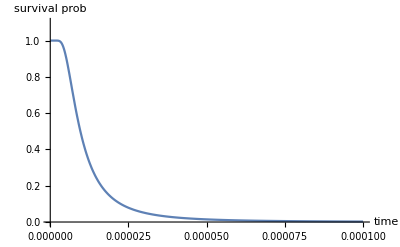

```mathematica
pv = (m/(2π kB T))^(3/2)4π v^2 Exp[- m v^2/(2 kB T)];
capfrac = Integrate[pv, {v, 0, vmax}];
params = {kB -> 1.38*10^-23, T -> Texp, m -> msr,  U0-> U0exp, w-> wexp};
cf = capfrac/.params;
Plot[cf, {t, 0, .0001}, PlotRange -> {0, 1.1}, AxesLabel->{"time", "survival prob"}]
```